```mathematica
fcogs ={};
nus={};
AESs={};
BESs={};
AE153s={};
BE153s={};
scanUps ={};
scanDowns={};
```

## Voltage Systematics

```mathematica
fittedDirectory = "C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=7-2\\2022-06-14 Voltage\\fit_result"
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=7-2\2022-06-14 Voltage\fit_result

```mathematica
SetDirectory[fittedDirectory]
voltages =FileNames["V*fit.csv"];
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=7-2\2022-06-14 Voltage\fit_result

```mathematica
vs ={};
fcogvs ={};
gammas={};
nuvs={};
AESvs={};
BESvs={};
AE153vs={};
BE153vs={};

For[i=1,i≤Length[voltages],i++,
voltageFit = Import[voltages[[i]]];
v=Around[voltageFit[[2,2]],voltageFit[[3,2]]];
fcogv = Around[voltageFit[[2,3]],voltageFit[[3,3]]];
gammav = Around[voltageFit[[2,4]],voltageFit[[3,4]]];
nuv = Around[voltageFit[[2,5]],voltageFit[[3,5]]];
AESv = Around[voltageFit[[2,6]],voltageFit[[3,6]]];
BESv = Around[voltageFit[[2,7]],voltageFit[[3,7]]];
BE153v = Around[voltageFit[[2,8]],voltageFit[[3,8]]];
AE153v = Around[voltageFit[[2,9]],voltageFit[[3,9]]];

AppendTo[vs,v];
AppendTo[fcogvs,fcogv];
AppendTo[gammas,gammav];
AppendTo[nuvs,nuv];
AppendTo[AESvs,AESv];
AppendTo[BESvs,BESv];
AppendTo[AE153vs,AE153v];
AppendTo[BE153vs,BE153v];

AppendTo[fcogs,voltageFit[[All,3]]];
AppendTo[scanUps,voltageFit[[All,3]][[4;;7]]];
AppendTo[scanDowns,voltageFit[[All,3]][[8;;]]];
AppendTo[fcogs,voltageFit[[All,3]]];
AppendTo[nus,voltageFit[[All,5]]];
AppendTo[AESs,voltageFit[[All,6]]];
AppendTo[BESs,voltageFit[[All,7]]];
AppendTo[BE153s,voltageFit[[All,8]]];
AppendTo[AE153s,voltageFit[[All,9]]];
]
```

```mathematica
voltageFit
```

{{,Voltage,fcog,gamma,isotope shift,AES,BES,BE153,AE153},{Mean value,300,4089.99,26.6517,-2975.99,-218.656,-292.772,-752.79,-96.8523},{error,0,0.156825,,6.13608,0.030652,0.604415,18.2909,1.01287},{,300,4090.16,19.1657,-2976.44,-218.673,-292.519,-752.841,-96.9099},{,300,4090.2,15.2858,-2975.6,-218.692,-293.481,-749.195,-96.7245},{,300,4090.21,16.4498,-2975.61,-218.655,-291.817,-750.232,-96.7441},{,300,4090.87,35.8862,-2976.63,-218.613,-293.161,-755.416,-96.8941},{,300,4089.31,22.9966,-2975.48,-218.692,-292.839,-750.985,-96.8676},{,300,4089.76,31.8477,-2976.51,-218.638,-292.5,-754.707,-96.8959},{,300,4089.58,44.4046,-2975.17,-218.626,-292.557,-754.087,-96.8398},{,300,4089.81,27.1768,-2976.51,-218.662,-293.3,-754.857,-96.9421}}

```mathematica
voltages
```

{V200fit.csv,V225fit.csv,V275fit.csv,V300fit.csv}

FittedModel[4090.19-0.000626482 x]

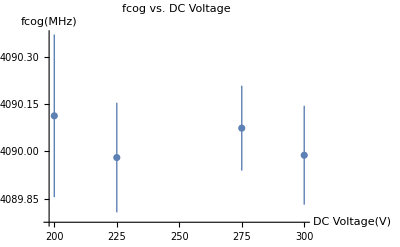

0.19323

```mathematica
lmv = LinearModelFit[Transpose[{vs,fcogvs[[All,1]]}],x,x]
Show[ListPlot[Transpose[{vs,fcogvs}],PlotRange->All,AxesLabel->{"DC Voltage(V)","fcog(MHz)"},PlotLabel->"fcog vs. DC Voltage"](*,Plot[lmv[x],{x,200,350}]*)]
lmv["RSquared"]
```

```mathematica
AESvs
```

{-218.760.04,-218.6610.026,-218.6270.023,-218.6560.031}

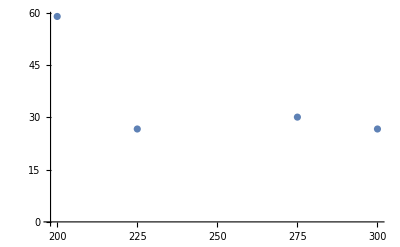

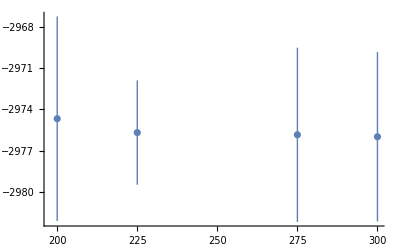

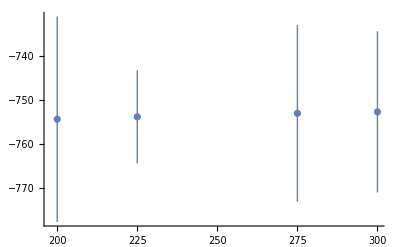

```mathematica
ListPlot[Transpose[{vs,gammas}],PlotRange->All]
ListPlot[Transpose[{vs,nuvs}],PlotRange->All]
ListPlot[Transpose[{vs,BE153vs}],PlotRange->All]
```

```mathematica
meansV ={Mean[fcogvs],Mean[gammas],Mean[nuvs]}
```

{4090.040.09,35.5746(√(^2))/2,-2975.63.0}

## Pressure Systematics

```mathematica
directoryPressure ="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=7-2\\2022-06-16 Pressure";
SetDirectory[directoryPressure]
pressures =FileNames["P*fit.csv"];
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=7-2\2022-06-16 Pressure

```mathematica
ps ={};
fcogps ={};
gammas={};
nups={};
AESps={};
BESps={};
AE153ps={};
BE153ps={};

For[i=1,i≤Length[pressures],i++,
pressureFit = Import[pressures[[i]]];
p=Around[pressureFit[[2,2]],pressureFit[[3,2]]];
fcogp = Around[pressureFit[[2,3]],pressureFit[[3,3]]];
gammap = Around[pressureFit[[2,4]],pressureFit[[3,4]]];
nup = Around[pressureFit[[2,5]],pressureFit[[3,5]]];
AESp = Around[pressureFit[[2,6]],pressureFit[[3,6]]];
BESp = Around[pressureFit[[2,7]],pressureFit[[3,7]]];
BE153p = Around[pressureFit[[2,8]],pressureFit[[3,8]]];
AE153p = Around[pressureFit[[2,9]],pressureFit[[3,9]]];
If[i==2,AppendTo[scanUps,voltageFit[[All,3]][[4;;7]]];
AppendTo[scanDowns,voltageFit[[All,3]][[8;;]]];];
AppendTo[ps,p];
AppendTo[fcogps,fcogp];
AppendTo[gammas,gammap];
AppendTo[nups,nup];
AppendTo[AESps,AESp];
AppendTo[BESps,BESp];
AppendTo[AE153ps,AE153p];
AppendTo[BE153ps,BE153p];

AppendTo[fcogs,pressureFit[[All,3]]];AppendTo[nus,pressureFit[[All,5]]];
AppendTo[AESs,pressureFit[[All,6]]];
AppendTo[BESs,pressureFit[[All,7]]];
AppendTo[BE153s,pressureFit[[All,8]]];
AppendTo[AE153s,pressureFit[[All,9]]];
]
```

FittedModel[4091.2-0.00627525 x]

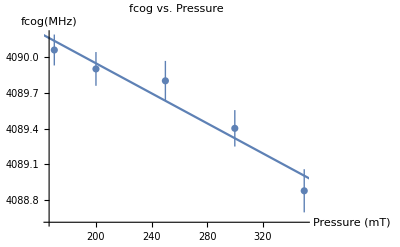

0.934415

```mathematica
lmp = LinearModelFit[Transpose[{ps,fcogps[[All,1]]}],x,x]
Show[ListPlot[Transpose[{ps,fcogps}],PlotRange->All,AxesLabel->{"Pressure (mT)","fcog(MHz)"},PlotLabel->"fcog vs. Pressure"],Plot[lmp[x],{x,150,400}]]
lmp["RSquared"]
```

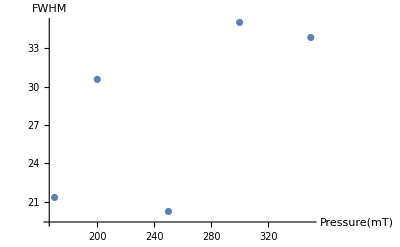

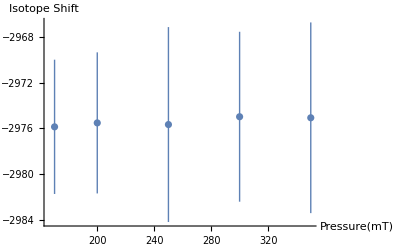

```mathematica
ListPlot[Transpose[{ps,gammas}],PlotRange->All,AxesLabel->{"Pressure(mT)","FWHM"}]
ListPlot[Transpose[{ps,nups}],PlotRange->All,AxesLabel->{"Pressure(mT)","Isotope Shift"}]
(*ListPlot[Transpose[{ps,AESps}],PlotRange->All,AxesLabel->{"Pressure(mT)","A151"}]
ListPlot[Transpose[{ps,BESps}],PlotRange->All,AxesLabel->{"Pressure(mT)","B151"}]
ListPlot[Transpose[{ps,AE153ps}],PlotRange->All,AxesLabel->{"Pressure(mT)","A153"}]
ListPlot[Transpose[{ps,BE153ps}],PlotRange->All,AxesLabel->{"Pressure(mT)","B153"}]
*)
```

```mathematica
meansP ={Mean[fcogps],Mean[nups]}
```

{4089.610.07,-2975.43.3}

## Power Systematics

```mathematica
directoryI="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=7-2\\2022-06-17 Laser Power\\fit_result";
SetDirectory[directoryI]
intensities =FileNames["s*fit.csv"];
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=7-2\2022-06-17 Laser Power\fit_result

```mathematica
ints ={};
fcogints ={};
gammas={};
nuints={};
AESints={};
BESints={};
AE153ints={};
BE153ints={};

For[i=1,i≤Length[intensities],i++,
intensityFit = Import[intensities[[i]]];
int=Around[intensityFit[[2,2]],intensityFit[[3,2]]];
fcogint = Around[intensityFit[[2,3]],intensityFit[[3,3]]];
gammaint = Around[intensityFit[[2,4]],intensityFit[[3,4]]];
nuint = Around[intensityFit[[2,5]],intensityFit[[3,5]]];
AESint = Around[intensityFit[[2,6]],intensityFit[[3,6]]];
BESint = Around[intensityFit[[2,7]],intensityFit[[3,7]]];
BE153int = Around[intensityFit[[2,8]],intensityFit[[3,8]]];
AE153int = Around[intensityFit[[2,9]],intensityFit[[3,9]]];

AppendTo[ints,int];
AppendTo[fcogints,fcogint];
AppendTo[gammas,gammaint];
AppendTo[nuints,nuint];
AppendTo[AESints,AESint];
AppendTo[BESints,BESint];
AppendTo[AE153ints,AE153int];
AppendTo[BE153ints,BE153int];
AppendTo[scanUps,intensityFit[[All,3]][[4;;7]]];
AppendTo[scanDowns,intensityFit[[All,3]][[8;;]]];

AppendTo[fcogs,intensityFit[[All,3]]];AppendTo[nus,intensityFit[[All,5]]];
AppendTo[AESs,intensityFit[[All,6]]];
AppendTo[BESs,intensityFit[[All,7]]];
AppendTo[BE153s,intensityFit[[All,8]]];
AppendTo[AE153s,intensityFit[[All,9]]];
]
```

FittedModel[4089.51+0.149477 x]

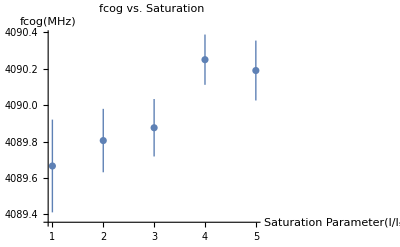

0.876208

```mathematica
lmi = LinearModelFit[Transpose[{ints,fcogints[[All,1]]}],x,x]
Show[ListPlot[Transpose[{ints,fcogints}],PlotRange->All,AxesLabel->{"Saturation Parameter(I/I_s)","fcog(MHz)"},PlotLabel->"fcog vs. Saturation"],Plot[lmi[x],{x,150,350}]]
lmi["RSquared"]
```

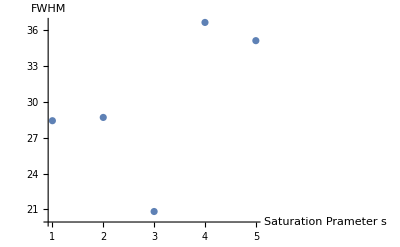

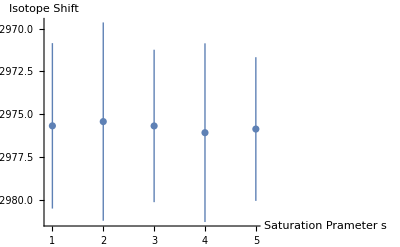

```mathematica
ListPlot[Transpose[{ints,gammas}],PlotRange->All,AxesLabel->{"Saturation Prameter s","FWHM"}]
ListPlot[Transpose[{ints,nuints}],PlotRange->All,AxesLabel->{"Saturation Prameter s","Isotope Shift"}]
```

```mathematica
meansP ={Mean[fcogints],Mean[nuints]}
```

{4089.960.08,-2975.72.2}

```mathematica
5146+652384520
```

652389666

```mathematica
Mean[Join[nuvs[[All]],nups[[All]],nuints[[All]]]]
```

-2975.61.7

```mathematica
Mean[Join[fcogints,fcogps,fcogvs]]
```

4089.860.05

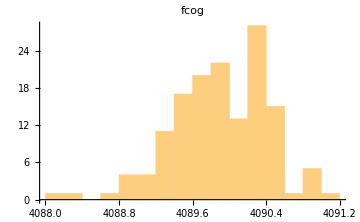

```mathematica
histFcog=Histogram[Flatten[fcogs[[All,4;;]]],11,PlotLabel->"fcog",ImageSize->Medium]
```

```mathematica
fcogUpsShifted=Flatten[scanUps]-Table[(Flatten[scanUps][[n]]-Flatten[scanDowns][[n]])/2,{n,1,Length[Flatten[scanUps]]}];
fcogDowns=Flatten[scanDowns]+Table[(Flatten[scanUps][[n]]-Flatten[scanDowns][[n]])/2,{n,1,Length[Flatten[scanUps]]}];
```

```mathematica
shift=(Mean[Flatten[scanUps]]-Mean[Flatten[scanDowns]])/2;
```

```mathematica
fcogShifted=Join[Flatten[scanUps]-shift,Flatten[scanDowns]+shift]
```

{4089.98,4090.04,4090.09,4090.21,4089.76,4089.94,4089.91,4089.88,4090.05,4089.99,4089.98,4090.48,4089.78,4089.82,4089.83,4090.49,4089.78,4089.82,4089.83,4090.49,4089.8,4089.54,4089.38,4089.9,4089.84,4089.92,4089.78,4090.,4090.15,4089.71,4090.09,4090.07,4090.47,4089.84,4090.39,4089.86,4090.15,4090.07,4089.88,4090.7,4090.18,4090.01,4090.19,4090.19,4089.82,4090.28,4090.33,4089.91,4089.9,4090.02,4090.,4090.16,4089.69,4090.14,4089.96,4090.19,4089.69,4090.14,4089.96,4090.19,4089.87,4089.52,4089.63,4089.69,4089.67,4089.72,4089.79,4089.72,4089.62,4089.82,4089.63,4089.92,4090.11,4090.28,4090.51,4090.53,4090.21,4090.39,4090.01,4090.12}

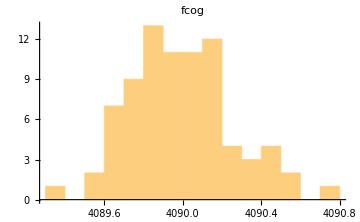

```mathematica
Histogram[fcogShifted,10,PlotLabel->"fcog",ImageSize->Medium]
```

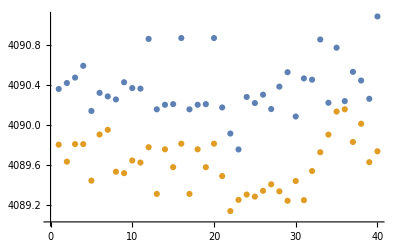

```mathematica
ListPlot[{Flatten[scanUps],Flatten[scanDowns]}]
```

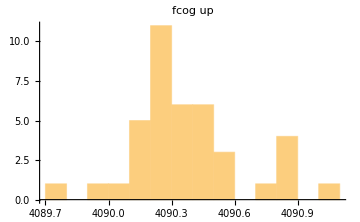

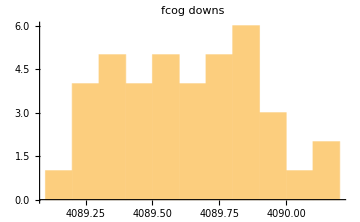

```mathematica
Histogram[Flatten[scanUps],10,PlotLabel->"fcog up",ImageSize->Medium]
Histogram[Flatten[scanDowns],10,PlotLabel->"fcog downs",ImageSize->Medium]
```

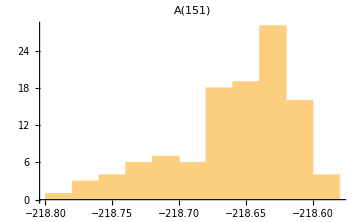

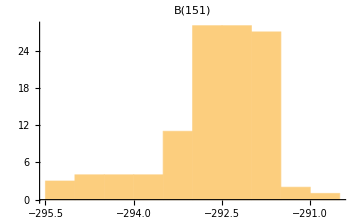

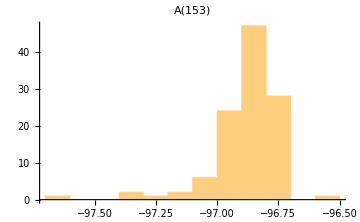

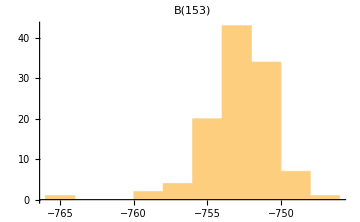

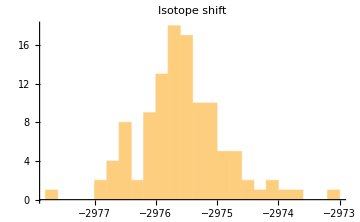

```mathematica
histA151=Histogram[Flatten[AESs[[All,4;;]]],10,PlotLabel->"A(151)",ImageSize->Medium]
histB151=Histogram[Flatten[BESs[[All,4;;]]],10,PlotLabel->"B(151)",ImageSize->Medium]
histA5153=Histogram[Flatten[AE153s[[All,4;;]]],11,PlotLabel->"A(153)",ImageSize->Medium]
histB153=Histogram[Flatten[BE153s[[All,4;;]]],10,PlotLabel->"B(153)",ImageSize->Medium]
histIso=Histogram[Flatten[nus[[All,4;;]]],15,PlotLabel->"Isotope shift",ImageSize->Medium]
```

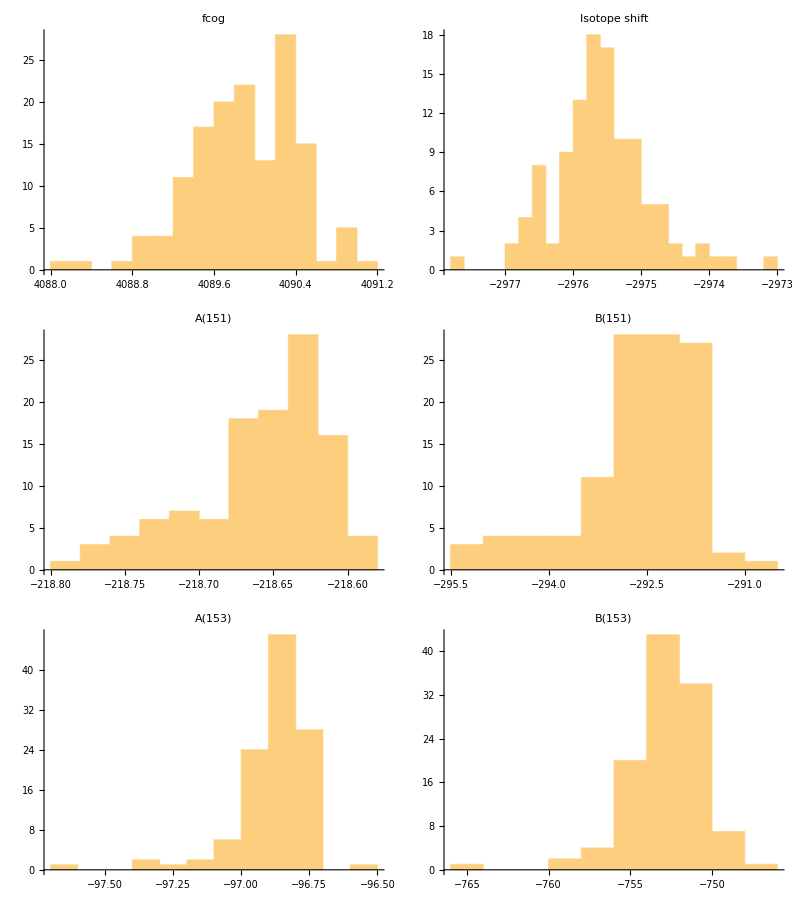

```mathematica
Grid[{{histFcog,histIso},{histA151,histB151},{histA5153,histB153}}]
```

```mathematica
Length[Flatten[fcogs[[All,4;;]]]]
```

144

```mathematica
Length[fcogs]
```

18

```mathematica
StandardDeviation[Flatten[nus[[All,4;;]]]]
Mean[Flatten[nus[[All,4;;]]]]
```

0.695709

-2975.57

```mathematica
fogerror=Max[{Mean[fcogs[[All,3]]],
StandardDeviation[Flatten[fcogs[[All,4;;]]]]}];
AESerror=Max[{Mean[AESs[[All,3]]],
StandardDeviation[Flatten[AESs[[All,4;;]]]]}];
BESerror=Max[{Mean[BESs[[All,3]]],
StandardDeviation[Flatten[BESs[[All,4;;]]]]}];
AE153error=Max[{Mean[AE153s[[All,3]]],
StandardDeviation[Flatten[AESs[[All,4;;]]]]}];
BE153error=Max[{Mean[BE153s[[All,3]]],
StandardDeviation[Flatten[BESs[[All,4;;]]]]}];
nuerror=Max[{Mean[nus[[All,3]]],
StandardDeviation[Flatten[nus[[All,4;;]]]]}];
```

```mathematica
result = {{Mean[Flatten[fcogs[[All,4;;]]]],fogerror},{Mean[Flatten[nus[[All,4;;]]]],nuerror},{Mean[Flatten[AESs[[All,4;;]]]],AESerror},{Mean[Flatten[BESs[[All,4;;]]]], BESError},{Mean[Flatten[AE153s[[All,4;;]]]],AE153error},{Mean[Flatten[BE153s[[All,4;;]]]], BE153error}};
TableForm[result,TableHeadings->{{"fcog","nu","AES","BES","AE153","BE153"},{"Mean","error"}}]
```

| Mean | error
fcog | 4089.9 | 0.524431
nu | -2975.57 | 6.02708
AES | -218.659 | 0.0445402
BES | -292.617 | 0.534554
AE153 | -96.8812 | 0.999318
BE153 | -752.731 | 19.5106